## Twisted Bilayer, Isotropic Forces, No Layer Coupling

```mathematica
ClearAll[ex, ey, n, latticepts,unitcellpts,dcutoff,bonds,segmentn,segments,qloop, freqs,D3x3]
```

## Layer Parameters

```mathematica
ebx={1,0,0};
eby={0,1,0};
lx=3;
ly=4;
lm=√(lx^2+ly^2);
θ=N[ArcTan[ly/lx]];
rot=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
etx=rot.ebx;
ety=rot.eby;
(*Moire*)
eMx=(√(lx^2+ly^2))*etx;
eMy=(√(lx^2+ly^2))*ety;
(*Inverse*)
Gbx=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eby)/(ebx.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eby);
Gby=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ebx)/(eby.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ebx);
Gtx=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ety)/(etx.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).ety);
Gty=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).etx)/(ety.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).etx);
GMx=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMy)/(eMx.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMy);
GMy=2π*(({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMx)/(eMy.({{0, -1, 0}, {1, 0, 0}, {0, 0, 1}}).eMx);
```

## Create Lattice and unit cell

```mathematica
n=50;
h=1;
δ=.01;
latticepts={};
unitcellpts={};
For[i=(-n )/2,i<=n/2,i++,
For[j=(-n)/2,j<=n/2,j++,
AppendTo[latticepts, i*ebx+j*eby];
AppendTo[latticepts,i*etx+j*ety+{0,0,h}];
If[-δ<=((i*ebx+j*eby)/Norm[eMx]^2).eMx<=1-δ&&-δ<=((i*ebx+j*eby)/Norm[eMy]^2).eMy<=1-δ,
AppendTo[unitcellpts, i*ebx+j*eby];
];
If[-δ<=((i*etx+j*ety)/Norm[eMx]^2).eMx<=1-δ&&-δ<=((i*etx+j*ety)/Norm[eMy]^2).eMy<=1-δ,
AppendTo[unitcellpts, i*etx+j*ety+{0,0,h}];
];
]
]
ListPointPlot3D[unitcellpts,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

## Generate Adjacent Unit Cells

```mathematica
dcutoff =√2;
(*Bilayer*)
unitcells={};
xmin =Min[unitcellpts.eMx/(√(eMx.eMx))]-dcutoff;
xmax =Max[unitcellpts.eMx/(√(eMx.eMx))]+dcutoff;
ymin=Min[unitcellpts.eMy/(√(eMy.eMy))]-dcutoff;
ymax=Max[unitcellpts.eMy/(√(eMy.eMy))]+dcutoff;
nxmin=Floor[xmin/(√(eMx.eMx))];
nxmax = Ceiling[xmax/(√(eMx.eMx))];
nymin=Floor[ymin/(√(eMy.eMy))];
nymax=Ceiling[ymax/(√(eMy.eMy))];
For[i=nxmin,i<=nxmax,i++,
For[j=nymin,j<=nymax,j++,
AppendTo[unitcells, i*eMx + j*eMy]
];
];
```

## Create List of Bonds Included

```mathematica
bonds={};
bondgraphics={};
Monitor[For[i=1,i<=Length[unitcellpts],i++,
For[j=1,j<=Length[unitcellpts],j++,
For[R=1,R<=Length[unitcells],R++,
d=Norm[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]];
If[d!=0&&d<=dcutoff&&Abs[unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]][[3]]<h/2,
dhat=1/d*(unitcellpts[[j]]+unitcells[[R]]-unitcellpts[[i]]);
AppendTo[bonds,{i, j,R,dhat,d}];
AppendTo[bondgraphics,Line[{unitcellpts[[i]],unitcellpts[[j]]+unitcells[[R]]}]];
];
]
]
],{i,j}]
Show[Graphics3D[bondgraphics],ListPointPlot3D[unitcellpts]]
```

-Graphics3D-

## Create Momentum Loop

```mathematica
segmentn=100;
segments={{0,0,0},.1*(1/2 GMx+1/2 GMy)};
qloop={};
For[s=1,s<Length[segments],s++,
For[i=1,i<=segmentn,i++,
AppendTo[qloop,segments[[s]]+i*((segments[[s+1]]-segments[[s]])/segmentn)]
]
]
ListPointPlot3D[qloop]
```

-Graphics3D-

## Main Loop

```mathematica
freqs={};
A=1;
λ=10;
Monitor[For[k=1,k<=Length[qloop],k++,
(*Momentum*)
q=qloop[[k]]; 
(*Dynamics Matrixes*)
DynamicsMatrix=ConstantArray[0,{Length[unitcellpts],Length[unitcellpts]}];
(*Loop over bonds*)
For[i=1,i<=Length[bonds],i++,
a1=bonds[[i]][[1]];
a2=bonds[[i]][[2]];
R=bonds[[i]][[3]];
dhat=bonds[[i]][[4]];
d=bonds[[i]][[5]];
D3x3=A*ⅇ^(-λ*d);
DynamicsMatrix[[a1,a1]]+=1*D3x3;
DynamicsMatrix[[a1,a2]]+=-D3x3*ⅇ^(I*unitcells[[R]].q);
];
AppendTo[freqs,ReverseSort[√(Eigenvalues[DynamicsMatrix])]]
]
,{k}]
```

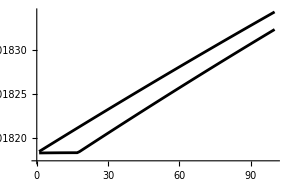

```mathematica
ListLinePlot[Table[Re[freqs[[;;,i]]],{i,1,2}],PlotStyle->{{Black}}]
```

## Analytic Results

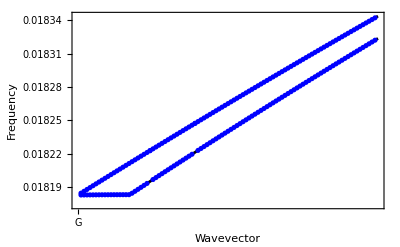

```mathematica
C1b=A*Sum[ⅇ^(-λ*n)(4-2Cos[n*qx]-2Cos[n*qy]),{n,1,dcutoff}]+A*Sum[If[√(n^2+m^2)<=dcutoff,ⅇ^(-λ*√(n^2+m^2))(4-4Cos[n*qx]Cos[m*qy]),0],{n,1,dcutoff},{m,1,dcutoff}];
C1t=A*Sum[ⅇ^(-λ*n)(4-2Cos[n*(qx*etx[[1]]+qy*etx[[2]])]-2Cos[n*(qx*ety[[1]]+qy*ety[[2]])]),{n,1,dcutoff}]+A*Sum[If[√(n^2+m^2)<=dcutoff,ⅇ^(-λ*√(n^2+m^2))(4-4Cos[n*(qx*etx[[1]]+qy*etx[[2]])]Cos[m*(qx*ety[[1]]+qy*ety[[2]])]),0],{n,1,dcutoff},{m,1,dcutoff}];
DM[qx_,qy_]:=Evaluate[({{C1b, 0, 0, 0, 0, 0}, {0, C1b, 0, 0, 0, 0}, {0, 0, C1b, 0, 0, 0}, {0, 0, 0, C1t, 0, 0}, {0, 0, 0, 0, C1t, 0}, {0, 0, 0, 0, 0, C1t}})];
analyticfoldedfreqs={};
nfolds=4;
For[k=1,k<Length[qloop],k++,
AppendTo[analyticfoldedfreqs,{}];
For[a=-nfolds,a<nfolds,a++,
For[b=-nfolds,b<nfolds,b++,
q=qloop[[k]]+a*GMx+b*GMy;
analyticfoldedfreqs[[-1]]=ReverseSort[Join[analyticfoldedfreqs[[-1]],ReverseSort[√Eigenvalues[DM[q[[1]],q[[2]]]]]]];
]
]
]
For[i=1,i<=Length[analyticfoldedfreqs],i++,
analyticfoldedfreqs[[i]]=DeleteDuplicates@*Flatten@analyticfoldedfreqs[[i]];
]
nbands=2;
Show[{ListLinePlot[Table[Re[freqs[[;;,i]]],{i,1,nbands}],PlotStyle->{{Black}},PlotRange->All],ListPlot[Table[analyticfoldedfreqs[[;;,i]],{i,1,nbands}],PlotStyle->{{Blue}}]},Frame->True,FrameTicks->{{Automatic,None},{{{0,"G"}},None}},FrameLabel->{{"Frequency",""},{"Wavevector",""}}]
```